## E = E ẑ, B = B ẑ

```mathematica
em=υ/2(B e kz vf χ)/(kx^2+ky^2+kz^2);
FullSimplify[Grad[em,{kx,ky,kz}]/.{kx->k Cos[ϕ] Sin[θ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]}]
```

{-(B e vf υ χ Cos[θ] Cos[ϕ] Sin[θ])/k^2,-(B e vf υ χ Cos[θ] Sin[θ] Sin[ϕ])/k^2,-(B e vf υ χ Cos[2 θ])/(2 k^2)}

```mathematica
Clear[B,Be,kx,ky,kz,s,cq,vf,k,v0,v1,v0dotΩ,vmdotΩ,enm,det];
krep={k->(-vf+√vf √(vf+4 cq ϵ))/(2 cq vf)};
ass={k,vf,cq,ϵ,μ}∈Reals && k>0 && vf>0 && cq>0 && ϵ>0 && μ>0;
Be={0,0,B};
BdotΩ=-ζ(B χ Cos[θ])/k^2;
v0=vf(1+2 cq k){Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ],Cos[θ]};
enm=υ(B e Cos[θ] vf χ)/(2 k);
vm={-(B e vf υ χ Cos[θ] Cos[ϕ] Sin[θ])/k^2,-(B e vf υ χ Cos[θ] Sin[θ] Sin[ϕ])/k^2,-(B e vf υ χ Cos[2 θ])/(2 k^2)};
v0dotΩ= -ζ((1+2 cq k) vf χ)/k^2;
vmdotΩ=υ ζ(B e vf Cos[θ])/(2 k^4);
(*f0'[en0]=-δ[Subscript[ϵ, χ,s]-μ];f0''[en0]=-δ'[Subscript[ϵ, χ,s]-μ];f0^(3)[en0]=-δ''[Subscript[ϵ, χ,s]-μ];*)
det=(k^2 Sin[θ])/(√vf √(vf+4 cq ϵ));
```

## linear disp band

```mathematica
(* -Graphics-;
-Graphics- *)
```

```mathematica
(* zz comp, along with the Drude term:*)
Clear[cond0,cond1,cond2,c0,c1,c2, δ, δp, δpp,cc1,cc2,cc3,cc4,cc5];
Print["Drude: indep of B terms"];(* v03^2 δ[ϵminμ] *)
c0=v0[[3]] v0[[3]] δ;
cond0=e^2 τ Integrate[det c0 ,{θ,0,π}]//FullSimplify
Print["B terms from I1 & I2 "];
c1=Simplify[(2v0[[3]] vm[[3]]-e BdotΩ (v0[[3]])^2) δ e^2 τ+ enm (v0[[3]])^2  δp e^2 τ-enm (v0[[3]])^2 e BdotΩ  δp e^2 τ+2enm v0[[3]] vm[[3]] δp e^2 τ+(e BdotΩ v0[[3]]-vm[[3]])^2 δ e^2 τ+(enm^2 v0[[3]] v0[[3]])/2 δpp  e^2 τ+(* -Graphics--> *)B^2 τ e^4(v0dotΩ)^2 δ]/.χ^2->1;
cond1[ζ_,υ_]=FullSimplify[ Integrate[det c1,{θ,0,π}]]/.χ^2->1
fac=(B^2 e^4 vf^(3/2) τ)/(60  √(vf+4 cq ϵ));
cc1=SeriesCoefficient[cond1[ζ,υ]/fac,{δ,0,1},{δp,0,0},{δpp,0,0}];
cc2=SeriesCoefficient[cond1[ζ,υ]/fac,{δ,0,0},{δp,0,1},{δpp,0,0}];
cc3=SeriesCoefficient[cond1[ζ,υ]/fac,{δ,0,0},{δp,0,0},{δpp,0,1}];
cc1 δ+cc2 δp+cc3 δpp==cond1[ζ,υ]/fac//FullSimplify
```

Drude: indep of B terms

(2 e^2 k^2 (1+2 cq k)^2 vf^(3/2) δ τ)/(3 √(vf+4 cq ϵ))

B terms from I1 & I2

(B^2 e^4 vf^(3/2) τ (k (1+2 cq k) vf υ (4 (3+6 cq k) δp ζ-4 δp υ+3 k (1+2 cq k) vf δpp υ)+2 δ (72 (ζ+2 cq k ζ)^2+7 υ^2-4 ζ (υ+2 cq k υ))))/(60 k^2 √(vf+4 cq ϵ))

True

```mathematica
Print["B terms from I3 and I4=I3"];
(* -Graphics-*)
c2=Simplify[
v0dotΩ(v0[[3]] +vm[[3]]-e v0[[3]]  BdotΩ)δ+v0[[3]]vmdotΩ δ+v0[[3]]enm v0dotΩ δp]/.χ^2->1;
cond2[ζ_,υ_]=2B τ e^3 Integrate[det c2,{θ,0,π}]//FullSimplify
fac=(B^2 e^4 vf^(3/2) τ)/(60  √(vf+4 cq ϵ));
cc4=SeriesCoefficient[cond2[ζ,υ]/fac,{δ,0,1},{δp,0,0},{δpp,0,0}];
cc5=SeriesCoefficient[cond2[ζ,υ]/fac,{δ,0,0},{δp,0,1},{δpp,0,0}];
cc4 δ+cc5 δp==cond2[ζ,υ]/fac//FullSimplify
```

B terms from I3 and I4=I3

-(2 e^4 (B+2 B cq k)^2 vf^(3/2) ζ τ (2 δ ζ+k vf δp υ))/(3 k^2 √(vf+4 cq ϵ))

True

```mathematica
Clear[int1];
intdrude=FullSimplify[(2 e^2 k^2 (1+2 cq k)^2 vf^(3/2) τ)/(3 √(vf+4 cq ϵ)) (* δ[ϵminμ] *)/.krep,Assumptions->ass]/.ϵ->μ
int1[ζ_,υ_]=(B^2 e^4 vf^(3/2) τ)/(60  √(vf+4 cq ϵ))FullSimplify[ cc1+cc4(*δ[ϵminμ]*)+(-1)D[ (cc2+cc5)((*fprime'[k]*)1)/(2 cq k vf+ vf),k](* δp[ϵminμ] *)+(-1)D[cc3(-2 cq(* fprime'[k]*))/((2 cq k+1)^3 vf^2)(*δpp[ϵminμ]*),k]+D[cc3((2 cq k+1) (*fprime''[k]*))/((2 cq k+1)^3 vf^2)(*δpp[ϵminμ]*),{k,2}]/.krep,Assumptions->ass]/.ϵ->μ
```

(e^2 √(1+(4 cq μ)/vf) (√vf-√(vf+4 cq μ))^2 τ)/(6 cq^2)

(2 B^2 cq^2 e^4 vf^(3/2) τ (32 ζ^2 (vf+4 cq μ)^2-14 vf ζ (vf+4 cq μ) υ-16 cq ζ μ √(vf (vf+4 cq μ)) υ-4 ζ √(vf^3 (vf+4 cq μ)) υ+3 √(vf^3 (vf+4 cq μ)) υ^2+2 vf (vf+7 cq μ) υ^2))/(15 (vf+4 cq μ)^(3/2) (√vf-√(vf+4 cq μ))^2)

```mathematica
SeriesCoefficient[int1[ζ,υ],{ζ,0,0}]//FullSimplify
```

(2 B^2 cq^2 e^4 vf^(3/2) (3 √(vf^3 (vf+4 cq μ))+2 vf (vf+7 cq μ)) τ υ^2)/(15 (vf+4 cq μ)^(3/2) (√vf-√(vf+4 cq μ))^2)

```mathematica
int1[ζ_,υ_]=(2 B^2 cq^2 e^4 vf^(3/2) τ (32 ζ^2 (vf+4 cq μ)^2-14 vf ζ (vf+4 cq μ) υ-16 cq ζ μ √(vf (vf+4 cq μ)) υ-4 ζ √(vf^3 (vf+4 cq μ)) υ+3 √(vf^3 (vf+4 cq μ)) υ^2+2 vf (vf+7 cq μ) υ^2))/(15 (vf+4 cq μ)^(3/2) (√vf-√(vf+4 cq μ))^2);int1bc=FullSimplify[ int1[1,0],Assumptions->ass]
int1omm=FullSimplify[(int1[1,1]-%),Assumptions->ass]
```

(64 B^2 cq^2 e^4 vf^(3/2) √(vf+4 cq μ) τ)/(15 (√vf-√(vf+4 cq μ))^2)

-(2 B^2 cq^2 e^4 vf^(3/2) (12 vf^2+42 cq vf μ+16 cq μ √(vf (vf+4 cq μ))+√(vf^3 (vf+4 cq μ))) τ)/(15 (vf+4 cq μ)^(3/2) (√vf-√(vf+4 cq μ))^2)

```mathematica
rep={cq->c,vf->Subscript[v, F],EF->μ,τrat->Subscript[τ, G]/τ};
FullSimplify[(τ B^2 cq e^4 (cq)^(3/2)  (τrat-1)vf^(3/2)√(vf^3 (4 cq EF+vf)) (6+√(vf/(4 cq EF+vf))) (vf+√(cq EF vf) (6+√(vf/(4 cq EF+vf)))))/(36 π^2 √(cq EF vf) (2 EF (cq vf)^(3/2)+cq vf^(3/2)√EF √(4 cq EF+vf)+vf^(3/2) √cq (vf-√(vf (4 cq EF+vf))))),Assumptions->{cq,vf, Ef}∈ Reals && vf>0 && cq>0 && Ef>0]
```

(B^2 e^4 (cq EF vf)^(3/2) √(4 cq EF+vf) (6+√(vf/(4 cq EF+vf))) (vf+√(cq EF vf) (6+√(vf/(4 cq EF+vf)))) τ (-1+τrat))/(36 EF^2 π^2 (2 cq EF √vf+vf^(3/2)-vf √(4 cq EF+vf)+√(cq EF vf) √(4 cq EF+vf)))

```mathematica
TeXForm[(-1+τrat)(6+√(vf/(4 cq EF+vf))) (vf+√(cq EF vf) (6+√(vf/(4 cq EF+vf))))/.rep]
```

\left(\frac{\tau _G}{\tau }-1\right) \left(\sqrt{\frac{v_F}{4 c \mu +v_F}}+6\right) \left(\sqrt{c \mu  v_F}
   \left(\sqrt{\frac{v_F}{4 c \mu +v_F}}+6\right)+v_F\right)

## Plots

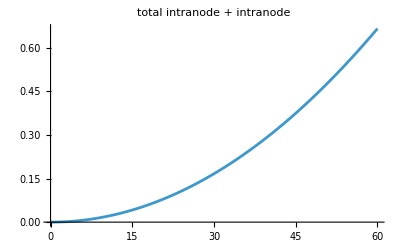

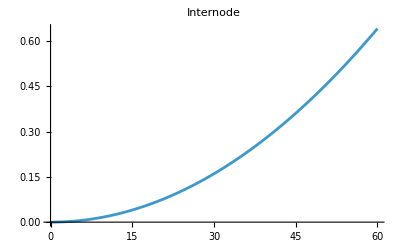

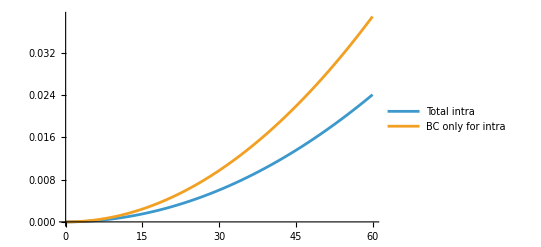

```mathematica
Clear[fn,finter,μ,drude];e=1;
drude[μ_,vf_,cq_]=1/(2π)^3(e^2 √(1+(4 cq μ)/vf) (√vf-√(vf+4 cq μ))^2 τ)/(6 cq^2);
fn[B_,μ_,vf_,cq_,{ζ_,υ_}]=1/((2π)^3 drude[μ,vf,cq])(2 B^2 cq^2 e^4 vf^(3/2) τ (32 ζ^2 (vf+4 cq μ)^2-14 vf ζ (vf+4 cq μ) υ-16 cq ζ μ √(vf (vf+4 cq μ)) υ-4 ζ √(vf^3 (vf+4 cq μ)) υ+3 √(vf^3 (vf+4 cq μ)) υ^2+2 vf (vf+7 cq μ) υ^2))/(15 (vf+4 cq μ)^(3/2) (√vf-√(vf+4 cq μ))^2);
(************************)

finter[B_,EF_,vf_,cq_,τrat_]=(B^2 e^4 (cq EF vf)^(3/2) √(4 cq EF+vf) (6+√(vf/(4 cq EF+vf))) (vf+√(cq EF vf) (6+√(vf/(4 cq EF+vf)))) τ (-1+τrat))/(36 EF^2 π^2 (2 cq EF √vf+vf^(3/2)-vf √(4 cq EF+vf)+√(cq EF vf) √(4 cq EF+vf)))/drude[EF,vf, cq];
mu=0.1;cqval=0.001;vfval=0.005;trat=100 ;
Plot[{fn[B,mu,vfval,cqval,{1,1}]+finter[B,mu,vfval,cqval,trat]},{B,0,60},PlotLabel->"total intranode + intranode"]
Plot[finter[B,mu,vfval,cqval,trat],{B,0,60},PlotLabel->"Internode"]
Plot[{fn[B,mu,vfval,cqval,{1,1}],fn[B,mu,vfval,cqval,{1,0}]},{B,0,60},PlotLegends->{"Total intra", "BC only for intra"}]

Clear[e];
```